# VYA - Přednášky

## 10. Přednáška

### Rozvoj periodické funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 5}]
Integrate[Vyraz , {t, t1, t1 + T}]
Integrate[{Vyraz * Cos[(2Pi * t)/T], Vyraz * Sin[(2Pi * t)/T]}, {t, t1, t1 + T}]
```

a[0]+a[1] Cos[(2 π t)/T]+a[2] Cos[(4 π t)/T]+a[3] Cos[(6 π t)/T]+a[4] Cos[(8 π t)/T]+a[5] Cos[(10 π t)/T]+b[1] Sin[(2 π t)/T]+b[2] Sin[(4 π t)/T]+b[3] Sin[(6 π t)/T]+b[4] Sin[(8 π t)/T]+b[5] Sin[(10 π t)/T]

T a[0]

{1/2 T a[1],1/2 T b[1]}

```mathematica
Quiet[Remove["Global`*"]];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

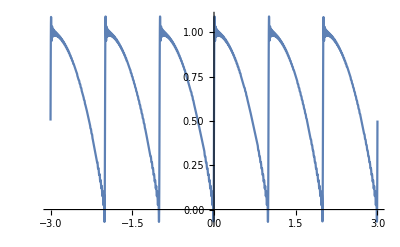

```mathematica
f[t_] := 1 - t^2;
T = 1;
a[0] := 1/T * NIntegrate[f[t], {t, 0 ,T}]
a[i_Integer] := 2/T * NIntegrate[f[t] * Cos[i * (2Pi * t)/T], {t, 0, T}]
b[i_Integer] := 2/T * NIntegrate[f[t] * Sin[i * (2Pi * t)/T], {t, 0, T}]
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 50}];
Plot[f[t], {t, 0, 1}];
Plot[Vyraz, {t, -3, 3}]
```

### Homogenní vedení

```mathematica
Quiet[Remove["Global`*"]];
```

### Řešení soustavy lineárních diferenciálních rovnic

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rov1 = y1'[x] == a * y1[x] + b * y2[x];
Rov2 = y2'[x] == c * y1[x] + d * y2[x];
DosazY2 = Solve[Rov1, y2[x]][[1]]
```

{y2[x]→(-a y1[x]+y1'[x])/b}

```mathematica
Dosaz = Union[DosazY2, D[DosazY2, x]]
```

{y2[x]→(-a y1[x]+y1'[x])/b,y2'[x]→(-a y1'[x]+y1''[x])/b}

```mathematica
Rovn = Simplify[Rov2 /. Dosaz]
```

1/b((b c-a d) y1[x]+(a+d) y1'[x]-y1''[x])==0

```mathematica
VysledRov = Numerator[Rovn[[1]]] == 0
VysledRov /. {Derivative[n_][y1][x] :> λ^n, y1[x] :> 1}
```

(b c-a d) y1[x]+(a+d) y1'[x]-y1''[x]==0

b c-a d+(a+d) λ-λ^2==0

```mathematica
FullForm[y1''[x]]
```

Derivative[2][y1][x]

```mathematica
?CoefficientArrays
```

```mathematica
?Thread
```

```mathematica
CoefficientArrays[{A + a*x - b*y - c*z == 0, B + d*x + e*y + f*z == 0}, {x, y, z}]
{vect, mat} = % // Normal
MatrixForm /@ %
Thread[mat. {x, y, z} + vect == 0]
```

{SparseArray[…],SparseArray[…]}

{{A,B},{{a,-b,-c},{d,e,f}}}

{(A
B),(a | -b | -c
d | e | f)}

{A+a x-b y-c z==0,B+d x+e y+f z==0}

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rov1 = y1'[x] == a * y1[x] + b * y2[x];
Rov2 = y2'[x] == c * y1[x] + d * y2[x];
{Vect,Mat} = -CoefficientArrays[{Rov1, Rov2}, {y1[x], y2[x]}]//Normal
```

{{-y1'[x],-y2'[x]},{{a,b},{c,d}}}

```mathematica
Det[Mat - λ * IdentityMatrix[2]]
```

-b c+a d-a λ-d λ+λ^2

### Metoda odhadu

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rovn = y''[x] + 5y'[x] + 6y[x] == 13*Exp[3x] + 2x + 1
RovnHomo = Rovn[[1]] == 0
RovnPrid = Rovn[[2]]
RovnChar = RovnHomo /.{Derivative[n_][y][x] :> λ^n, y[x] :> 1}
```

6 y[x]+5 y'[x]+y''[x]==1+13 ⅇ^(3 x)+2 x

6 y[x]+5 y'[x]+y''[x]==0

1+13 ⅇ^(3 x)+2 x

6+5 λ+λ^2==0

```mathematica
Solve[RovnChar]
y[x_] := k * Exp[3x]
RovnHomo[[1]]
Coefficient[RovnPrid, Exp[3x]] == RovnHomo[[1]] // Solve[#, k] &
```

{{λ→-3},{λ→-2}}

30 ⅇ^(3 x) k

{{k→(13 ⅇ^(-3 x))/30}}

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Rovn = y''[x] + 5y'[x] + 6y[x] == 13*Exp[-3x] + 2x + 1
RovnHomo = Rovn[[1]] == 0
RovnPrid = Rovn[[2]]
RovnChar = RovnHomo /.{Derivative[n_][y][x] :> λ^n, y[x] :> 1}
```

6 y[x]+5 y'[x]+y''[x]==1+13 ⅇ^(-3 x)+2 x

6 y[x]+5 y'[x]+y''[x]==0

1+13 ⅇ^(-3 x)+2 x

6+5 λ+λ^2==0

```mathematica
Solve[RovnChar]
y[x_] := k * x * Exp[-3x]
RovnHomo[[1]]
Coefficient[RovnPrid, Exp[-3x]] == RovnHomo[[1]] // Solve[#, k] &
```

{{λ→-3},{λ→-2}}

-6 ⅇ^(-3 x) k+15 ⅇ^(-3 x) k x+5 (ⅇ^(-3 x) k-3 ⅇ^(-3 x) k x)

{{k→-13 ⅇ^(3 x)}}

### Úkol 10

https://youtu.be/eETd54BUjoI?t=5228
Okomentovaný postup metody odhadu